```mathematica
(*
Brendan Morgan
905 391 452
Extra Credit, Homework 6 Problem 7
*)

(*This assumes a 2D case, because I believe the inclination of orbits is not very relevant for showing the effect of a flyby.*)
```

```mathematica
Remove["Global`*"]
SetAttributes[{m1, m2,m3,G},Constant]; 
$Assumptions = { Element[{m1, m2,m3,G},Reals] && m1>0 && m2 > 0  && m3>0 && G>0};

T1 = 1/2*m1*(x1'[t]^2+y1'[t]^2);
T2 = 1/2*m2*(x2'[t]^2+y2'[t]^2);
T3 = 1/2*m3*(x3'[t]^2+y3'[t]^2);

U[xA_,yA_,xB_,yB_,mA_,mB_]=-G*mA*mB/(Sqrt[(xA-xB)^2+(yA-yB)^2]);
U12=U[x1[t],y1[t],x2[t],y2[t],m1,m2];
U13=U[x1[t],y1[t],x3[t],y3[t],m1,m3];
U23=U[x2[t],y2[t],x3[t],y3[t],m2,m3];
 
lag=(T1+T2+T3)-(U12+U13+U23)//Simplify;

EL[q_] :=  D[lag,q] - Dt[   D[lag,  D[q,t]], t ] == 0;

EqnsOfMotion={EL[x1[t]],EL[y1[t]],EL[x2[t]],EL[y2[t]],EL[x3[t]],EL[y3[t]]};
GenCoords={x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]};

Print["Lagrangian: ", lag];
```

Lagrangian: 1/2 ((2 G m1 m2)/(√((x1[t]-x2[t])^2+(y1[t]-y2[t])^2))+(2 G m1 m3)/(√((x1[t]-x3[t])^2+(y1[t]-y3[t])^2))+(2 G m2 m3)/(√((x2[t]-x3[t])^2+(y2[t]-y3[t])^2))+m1 (x1'[t]^2+y1'[t]^2)+m2 (x2'[t]^2+y2'[t]^2)+m3 (x3'[t]^2+y3'[t]^2))

```mathematica
(***************************************************************************)
(*Scenario A*)

G=6.6743*10^-20; (* km^2 kg^-1 s^-1 *)
m1 = 1.989*10^30;(*Sun Mass*)
m2=5.972*10^24; (*Earth Mass*)
m3=1.898*10^27;(*Jupiter Mass*)
EndTimeA=0.5*10^9; (*Seconds*)
TimeStepA=10^4;

SunEarthJupiter={x1[0]==0,y1[0]==0,x2[0]==147.1*10^6,y2[0]==0,x3[0]==740.5*10^6,y3[0]==0,
			x1'[0]==0,y1'[0]==0,x2'[0]==0,y2'[0]==30.29,x3'[0]==0,y3'[0]==13.72};

numericA=NDSolve[{EqnsOfMotion,SunEarthJupiter},GenCoords,{t,0,EndTimeA,TimeStepA}][[1]];

Ax1[t_]=x1[t]/.numericA;//Simplify
Ay1[t_]=y1[t]/.numericA;//Simplify
Ax2[t_]=x2[t]/.numericA;//Simplify
Ay2[t_]=y2[t]/.numericA;//Simplify
Ax3[t_]=x3[t]/.numericA;//Simplify
Ay3[t_]=y3[t]/.numericA;//Simplify

Sun[t_]:=Graphics[{PointSize[0.05],Yellow,Point[{Ax1[t],Ay1[t]}]}];
Earth[t_]:=Graphics[{PointSize[0.01],Cyan,Point[{Ax2[t],Ay2[t]}]}];
Jupiter[t_]:=Graphics[{PointSize[0.03],Orange,Point[{Ax3[t],Ay3[t]}]}];

pix[t_]:=Show[Sun[t],Earth[t],Jupiter[t],Axes-> False,PlotRange->{{-10^9,10^9},{-10^9,10^9}},Background->Black,ImageSize->Large];

Animate[pix[t],{t,0,EndTimeA,TimeStepA}]
Print["The animation above shows Earth and Jupiter orbiting the Sun. 
Sizes of the bodies are obviously not to scale, but the sizes of the orbits are to scale. 
Real orbital parameters taken from: https://nssdc.gsfc.nasa.gov/planetary/factsheet/index.html
You can see the Sun move slightly upwards under the influence of the two planets over the course of the animation (about 15 years)."];
```

The animation above shows Earth and Jupiter orbiting the Sun. 
Sizes of the bodies are obviously not to scale, but the sizes of the orbits are to scale. 
Real orbital parameters taken from: https://nssdc.gsfc.nasa.gov/planetary/factsheet/index.html
You can see the Sun move slightly upwards under the influence of the two planets over the course of the animation (about 15 years).

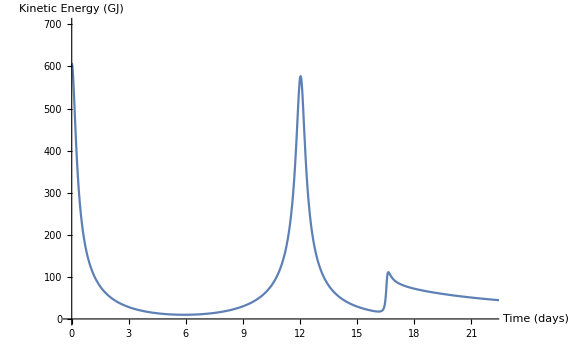

The animation above shows the Moon orbiting the Earth, and the SpaceX Starship en route to Mars, currently in a cislunar parking orbit.
The Starship uses a lunar flyby ~16 days into its mission to save on its Δv budget, the vast majority of which it already used in its trans-Mars injection burn.
The Starship's kinetic energy more than quintuples during its lunar flyby, from around 20 gigajoules to around 100 gigajoules.
Sizes of the bodies are not to scale, but the sizes of the orbits are to scale.

```mathematica
(***************************************************************************)
(*Scenario B*)

G=6.6743*10^-20; (* km^2 kg^-1 s^-1 *)
m1=5.972*10^24; (*Earth Mass*)
m2=7.348*10^22;(*Moon Mass*)
m3=85000;(*Starship Mass*)
EndTimeB=2*10^6; (*Seconds*)
TimeStepB=100;

EarthMoonStarship={x1[0]==0,y1[0]==0,x2[0]==363300,y2[0]==0,x3[0]==35000,y3[0]==35000,
			x1'[0]==0,y1'[0]==0,x2'[0]==0,y2'[0]==1.082,x3'[0]==-2.675,y3'[0]==2.670};

numericB=NDSolve[{EqnsOfMotion,EarthMoonStarship},GenCoords,{t,0,EndTimeB,TimeStepB}][[1]];

Bx1[t_]=x1[t]/.numericB;//Simplify
By1[t_]=y1[t]/.numericB;//Simplify
Bx2[t_]=x2[t]/.numericB;//Simplify
By2[t_]=y2[t]/.numericB;//Simplify
Bx3[t_]=x3[t]/.numericB;//Simplify
By3[t_]=y3[t]/.numericB;//Simplify

Earth[t_]:=Graphics[{PointSize[0.04],Cyan,Point[{Bx1[t],By1[t]}]}];
Moon[t_]:=Graphics[{PointSize[0.01],Yellow,Point[{Bx2[t],By2[t]}]}];
Starship[t_]:=Graphics[{PointSize[0.005],White,Point[{Bx3[t],By3[t]}]}];

Orbits[t_]:=Show[Earth[t],Moon[t],Starship[t],PlotRange->{{-700000,700000},{-700000,700000}},Background->Black,ImageSize->Large];

Animate[Orbits[t],{t,0,EndTimeB,TimeStepB}]
Kinetic[t_]:=(1/2*m3*(Bx3'[t]^2+By3'[t]^2))/1000;
Potential[t_]:=(-G*m3*m1/(Sqrt[(Bx3[t]-Bx1[t])^2+(By3[t]-By1[t])^2])-G*m3*m2/(Sqrt[(Bx3[t]-Bx2[t])^2+(By3[t]-By2[t])^2]))/1000;
MoonKinetic[t_]:=(1/2*m2*(Bx2'[t]^2+By2'[t]^2));

Plot[Kinetic[t*86400],{t,0,EndTimeB/86400},AxesLabel->{"Time (days)", "Kinetic Energy (GJ)"},PlotRange->{{0,22},{0,700}},AxesOrigin->{0,0},ImageSize->Large]
(*Plot[Potential[t*86400],{t,0,EndTimeB/86400},AxesLabel->{"Time (days)", "Potential Energy (GJ)"},AxesOrigin->{0,0},ImageSize->Large]*)

Print["The animation above shows the Moon orbiting the Earth, and the SpaceX Starship en route to Mars, currently in a cislunar parking orbit.
The Starship uses a lunar flyby ~16 days into its mission to save on its Δv budget, the vast majority of which it already used in its trans-Mars injection burn.
The Starship's kinetic energy more than quintuples during its lunar flyby, from around 20 gigajoules to around 100 gigajoules.
Sizes of the bodies are not to scale, but the sizes of the orbits are to scale."];
```